```mathematica
Ber[m_,r_]:=r^m(r^-1 m)!/(m^m(m(r^-1-1))!)
```

```mathematica
legplaced=Placed[LineLegend[{1,0.8,0.6,0.4,0.2},LegendFunction-> (Labeled[Panel[#],"Load Factor",Top]&)],Right]
```

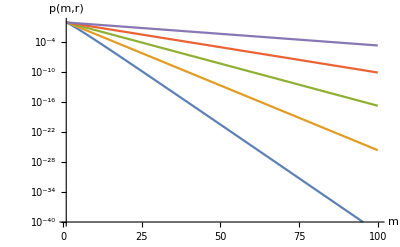

```mathematica
logplotber=LogPlot[
	{Ber[m,1],Ber[m,.8],Ber[m,.6],Ber[m,.4],Ber[m,.2]},{m,1.,100.},
	PlotRange->{10^-40,1},
	PlotLegends-> legplaced,
	AxesLabel->{m,p[m,r]}]
```

```mathematica
qBer[m_,r_]:=1-Ber[m,r]
```

```mathematica
fN[n_,m_,r_]:=qBer[m,r]^(2^n-1)(1-qBer[m,r]^(2^n))
```

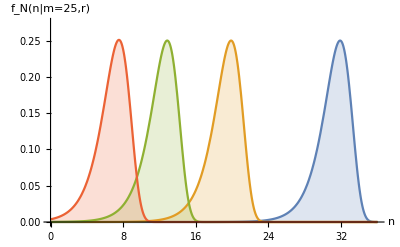

```mathematica
plotfn=Plot[
	{fN[n,25,1],fN[n,25,.8],fN[n,25,.6],fN[n,25,.4]},{n,0,36},
	Filling->Automatic,
	PlotRange->{0,.275},
	PlotLegends-> legplaced,
	AxesLabel->{n,"f_N(n|m=25,r)"}]
```

```mathematica
ExpN[m_,r_,nn_]:=Sum[n*fN[n,m,r],{n,0,nn}]//N
```

```mathematica
data5=Table[{rr,ExpN[5,rr,15]},{rr,0.05,1,.05}]
data10=Table[{rr,ExpN[10,rr,30]},{rr,0.05,1,.05}]
data20=Table[{rr,ExpN[20,rr,32]},{rr,0.05,1,.05}]
```

```mathematica
legListPlot=PointLegend[{5,10,20},
LegendMarkers->{Automatic},LegendFunction-> (Labeled[Panel[#],"Members",Top]&)]
```

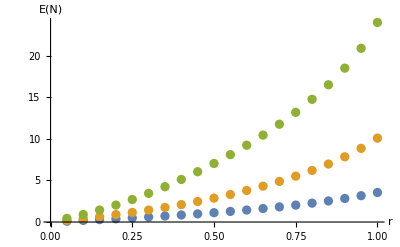

```mathematica
ListPlot[{data5,data10,data20},
AxesLabel->{r,"E"[N]},
PlotLegends->legListPlot]
```

```mathematica
datamrhalf=Table[{mm,ExpN[mm,.5,1.25*mm]},{mm,5,35,5}]
datamrthreeq=Table[{mm,ExpN[mm,.75,1.25*mm]},{mm,5,35,5}]
datamfull=Table[{mm,ExpN[mm,0.95,1.25*mm]},{mm,5,35,5}]
```

{{5,1.12201},{10,2.87212},{15,4.89902},{20,7.04956},{25,9.24396},{30,11.4519},{35,13.6638}}

{{5,2.03507},{10,5.516},{15,9.33225},{20,13.2019},{25,17.0788},{30,20.9571},{35,24.836}}

{{5,3.15982},{10,8.85557},{15,14.8549},{20,20.9164},{25,26.9721},{30,33.0343},{35,39.1002}}

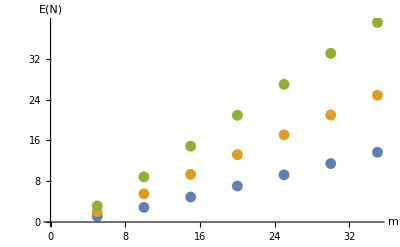

```mathematica
lfplot=ListPlot[{datamrhalf,datamrthreeq,datamfull},
AxesLabel->{m,"E"[N]},
PlotLegends-> Placed[LineLegend[{.5,0.75,0.95},LegendFunction-> (Labeled[Panel[#],"Load Factor",Top]&)],Right]]
```

```mathematica
Export["lfplot.eps",lfplot]
```

lfplot.eps

```mathematica
BerP[m_]:=Exp[-m]*(2*π*m)^(.5)//N
```

```mathematica
qBerP[m_]:=1-BerP[m]//N
```

```mathematica
fNP[n_,m_]:=qBerP[m]^(2^n-1)(1-qBerP[m]^(2^n))//N
```

```mathematica
ExpNP[m_,nn_]:=Sum[n*fNP[n,m],{n,0,nn}]//N
```

```mathematica
datamfull=Table[{mm,ExpNP[mm,1.5*mm]},{mm,5,35,5}]
```

{{5,3.57702},{10,10.1116},{15,17.0285},{20,24.0344},{25,31.087},{30,38.1689},{35,45.2749}}

```mathematica
datalarge=Table[{mm,ExpNP[mm,2*mm]},{mm,5,37}]
```

{{5,3.57746},{6,4.79768},{7,6.08121},{8,7.40372},{9,8.7501},{10,10.1116},{11,11.4832},{12,12.8621},{13,14.2466},{14,15.6357},{15,17.0285},{16,18.4246},{17,19.8236},{18,21.2251},{19,22.6287},{20,24.0344},{21,25.4419},{22,26.8511},{23,28.2617},{24,29.6737},{25,31.087},{26,32.5014},{27,33.9168},{28,35.3333},{29,36.7507},{30,38.1689},{31,39.5881},{32,41.0082},{33,42.4288},{34,43.8471},{35,45.2749},{36,46.7131},{37,48.0823}}

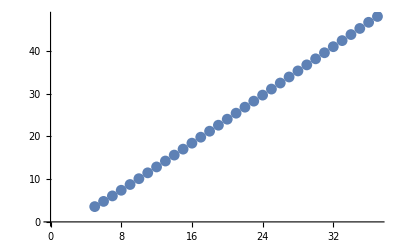

```mathematica
ListPlot[datalarge]
```

```mathematica
Fit[datalarge,{1,m},m]
```

-3.86314+1.40047 m

```mathematica
Fit[datamrhalf,{1,m},m]
```

-1.26106+0.422356 m

```mathematica
Fit[results2,{m},m]
```

Fit::fitd: First argument results2 in Fit is not a list or a rectangular array.

Fit[results2,{m},m]

```mathematica
ELB[m_]:=1/Log[2]*m//N
```

```mathematica
allresults=Join[results0,results,results2,results3,results4,results5]
```

Join[results0,results,results2,results3,results4,results5]

```mathematica
Table[{m,ELB[m]},{m,1500,2000}]
```

```mathematica
ListPlot[{results5,Table[{m,ELB[m]},{m,1500,2000}]}]
```

```mathematica
eval[m_,nx_]:=Sum[N[qBer[m,1],1000]^(2^n-1),{n,1,nx}]
```

```mathematica
evalr[m_,r_,nx_]:=Sum[N[qBer[m,r],1000]^(2^n-1),{n,1,nx}]
```

```mathematica
data_all=Table[{mm,eval[mm,1.5*mm]},{mm,100,2000,100}]
```

General::unfl: Underflow occurred in computation.

General::stop: Further output of General :: unfl will be suppressed during this calculation.

{{100,138.28787969033340030447516095047282250591315805706417978590098027480081562403166292656144584416972257488177794233679845139892759848237016692395828394701104520801027846859891522007100062364509859866595977881993743620014550975555001742971139326233034279784346678833401805877745376410730944319140340572620529804204870569666271129348855027258611125220302625935693142814907197214375406185922346267994551685399081066269554493231360056866787485771510133137935493593465378877332203587344135477520741889915505652381462552189777830457974379539506055785819558272313571298589392945356187315451152542398528939880017868505741613993817739849908484443821748738417615242637898275730807096298999741057127187354355563386583916201665429847296641044150232622830690845869897829677985118167808808700005354208884782348894733640774433620009965029723180933614680563456047602618039649189635198956521772573744908407291457749141036022265837691168166997208161079821855229747931377644179174},{200,282.0579862915131992542245800209510984400617621210664237777520780802678424354870928055793633451183375246869286272224656259951123577903847119176660931037816475489256672501596179497566375377472542508731701724960310210784206924131277509205934001106961511808908572777504516526379342085415849962393772151978925592517596656267886007126919057924724366766921795856923880765255685391919706671736670322481823286199845719542515146265508281300832090011522263954184592176638060134757679746885897121263017580549567529064411024292196761784087555637598853126394166665276230474817826021761541525606853213170806489191971656042050530365100830794459441837234147169209134382963964038685363806619000085997900702116961025050075429493299376255806562321993530663153370843958463521834403973336205320277645428875169927898731324590337428405212393961469453722484157485541508072479568715990588180559668277914089846065705778418236375129515225826367},{300,426.035209490512983951795695388430273988364578366953412006674269208623878504118828614678437041482229975082314459573505396694414272625562720044612029125808361659657197287590121864029755397510795049172997049667124755665544394196270960682431349238418788460611143062001552400849002726814429942737257659537012979546087333347198704918771992952395593410722699437281783835622091184569478000077052321452399941468336221585284038243907967911532313156342436111375919466660424220411530013569032560591532698412167959953011139275116566309530491311137302286564346073734643194451695597105703321248243528990726692846466568569444746685485222027580027898786607416667874857136804906336319016070063643587015488416746984445798447397223025758319973158840102364236361251298390054235546136398102905782907065322712627029168298301048868881465543286959249634018465628592269368761873090281824715962078381},{400,570.09729497816511075383828372402360670835888516438520786647293143726470094227886470527989163824840152714118227869276846715380367255623587714898259838884553419485845524842160481932933292818484182838234584444028185221382515300664738703593586964909338239396458922698624878266747220931770555687315780362369315927926353382045141393539769567392378700092931681107267541355691701389216096536487651101696955093170943724206883872418278867569470370310264526054910937017483127233280606614799375414508598395964655401695035539170464666128305027024109255065511273474415957961208141713272061026396425606367373386359236748645851727012629319517900131262098847626815586470916604170070194555092580357981781370060131190681461260558917670550502404481753688869783268447868874430755258411821740605992612799700291079992488152718594714178615175734343266064},{500,714.2058945377242513929733460092651471523044790618104755736788407819640452140899689587633261526067226304584984817646831910087641540799828888378994052201111567874738834762451517946218749272244150586474878922300097448589320265834143035696999755879025337462531942202857027316763792093685201067034070152499791727512553129465082545967767016841142603398519637688175706579686965210806259714736323944340032542064589908634485213634870993219938315333771750882404690654526468583335439604346557964613063165642521117518450819760218684581805320529763705474287739516461419872804384089288834926650080122061427504523384066464760508705858948354329937173167542747221892024695124986004436294229650082011773677085685351335332412867481233407210841942980235461710670691649136686955691594850565507055502463297767},{600,858.34392020197867166642562657856855008446288529022375554731365576470780515942237177611823771848741566576810538070784184836836472311791834333993286299372719710480820681122920834970717384761284151556100074757048630647401731258382042949085662420441365998751989019164965267702498655357207022480173665624988559850517625751144275822764657484899403734285675780144846817886033021126794285423107818406680339676039257534992521619935270957671727590174353397988713371063470337387055612014944667586587490483755531826508186265930142080789436599279369069337525396367072751035795275116408362023424417534301255648895746877539725454392443394964616339595574532461596991842296916066085694533252318883050241874135996295722576780072922430287569198604605133058101756},{700,1002.502255591123537858664185648857779199493608998216932484787217273631998864215289956991496366058724004548794431965312412490428678454853325405122624588558342080297212637379098965789178340835337118594084648656788250684654868141421256313712764488508760485624467453672309051253451194312179279298424804882693870610452832965318093183415564213910747381305957412585700622330758929935544497032294039979838211368136058970486086768111076474351246982696683727354056073739812042071050946463634180003031816323605949865745947116579105440628661706866898801090501956102331250025837738585044691773675555526805084993866523767005193646161540632271761030925793641821943308591230131002205341073761442774418072612623755482},{800,1146.67545894210365312604152205269780926258907595177161812622753698109530893695939124245912689540869726569186624246588296777121116695550390351100396964776479069403364909323611111329596009869076347241190992561401116493351957341215789406433781908488259249963303724947669330940226633854032617438830156802049621577632446420536934022603407021294124605980714855283214123429192261118739072736546144050540966101145400657344914484983396137776619520222466994260347955023360814162445575194006909911705951752327443243330614117999925809851856919376256764340140589065510447013589855149895409793730991058856258691371021849056993647758586664855539401085423489802500176233754},{900,1290.86001890192656008157267872782653695952931913111234405036023105773223378904104524804275258481066237751577543229134756641993747782705315586782593294828119554943178020829742272131385461927531640297540773663263477419697358583891840189128781243161347246622007626546579493005368721611370916247784635522115291789526376548615984658747915292750203984193027633823923000496688670025067361608166587001533852933093740941002495561748784687521643515365335219737913060911142770192809230641014527426025812772401932268735641020159432421373465558561629310729453333057522346973613862419868451567198787284868327729723128419184234},{1000,1435.0535358529823558707954021975153999069862434343922363290921212854534470836711185132735979480397036268844478020109057565114252409479721858213531372295536530497967459099489910097634860423890246120703219464122005702188351813033749652439321585384123411518318406186935881662886047796361931208175538221415708410622798895922458103058795209177212465234367499030543000745448616733676401729665791309879916443617452014490316248064967247393588927886692942170408602481814373542022497417942581052402354158045725415441677760601962659360384044489078896436150081828113025355953400325},{1100,1579.2542980400785334875032556080463236588186842319044699296634070635405831255351455349996098480071503422606881901487238182672564308123184818873458093759706638390677040764213406254499682390408115351471101459723823142238806209862492521773525073951489999679356135714543868526676084258102051049336767351075182568338863961509313737472944785364248041141248501139752559764853795060789803889489237333945820728341041428373663212764428670851925427773246210434411846705281940671239817530690621669355200501427740477151598041233195658395663},{1200,1723.46104399179685812613169048011225574286725577007942111963144178625134152786880226140088788461779339876020314881735037210908280498088435326135009561594323317579297544792869298509629260396720416812660122531135562409567677465569184712368404995648346941877287135297746146279611861902152234563012721745436927084283950797979540464291897434762475782869536580765739927257276750952810736565477203321248700360431516285540112842806222830692901391974665981609848587325973589115685947367446095},{1300,1867.6728173101588876843087099455065951744728968978791417877510054141110241155286735838164444029444368330886983169478720580097107812596714816165359986037997971834302385413007725109615709269760353045265405964321528450361061010260838972051368963011055497800196975352892446019463683205928050095534015470686489428106241342838742706322500776706772070509607154285010576701840250603609170382916647865628897090726520108764100695123114751185890576022},{1400,2011.888872353251894050460753794739837347308347826843075640170117719802835890794043300236591739641898848818604538263973558440230467078319326110063871357773518413098967734394429978063644818458492868769662751696127182490068030828175789713934310940077220329677501403243186129905606329881406364662429185757455031467629089344231920858018656221936688017511505402727889121977917778332288765504203044420527},{1500,2156.1086150374756682078063573291422221811585728826713895848097503187816917250720552500486797723315342041732486269621220432077191273983099945805565600465896729312925604211787172838907359654706743431565652432496765172075695879882651094221764015194661043135509348262791785314082663422384424616884913113726084572592812076414756904023975173063065343551982273},{1600,2300.33156769490038633822485325277366519402159205506722203066161346193868559008362729442929021472705913711969974584814300512169533927617331098327036812098751073769066244323018107267108333804557481143571836867982817790934462232414186038331245685317494825591173997939424184957292741731233313541741287575297512762},{1700,2444.5573434602550470084647191633549893048039041254115538746401403218067894465646574642500916375808972568314840026953448106040183364639099120117948538443823532542785787887144366209768403143815038234230373615342768931835796848664125415886542844699386889036009742856955},{1800,2588.785621768728707750069275997908180281246718754765753106820852696287509359063364353986636764504607174431834498464727060563810325650895938573470922296673608152825309747430827566760434249557377075393751356387341591583876195},{1900,2733.01612984299181224930993699180365745426069204535198314669735204581022749774768129466465933733706636743732350361647340640791777576894090951861417497083450130101133452506483193694},{2000,2877.248635837497764694745068804324925258233383541291124331419002541631519022329853381968758972942890064972520724120851891670465088279924}}

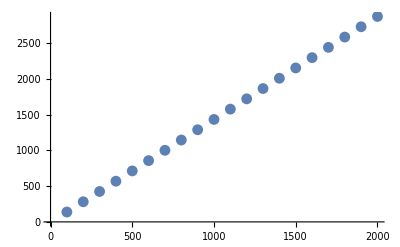

```mathematica
ListPlot[dataall]
```

```mathematica
Fit[dataall,{m},{m}]
```

Fit::fitd: First argument dataall in Fit is not a list or a rectangular array.

Fit[dataall,{m},{m}]

```mathematica
p[m,r]
```

p[m,r]